```mathematica
FullForm[a b + c d]
```

Plus[Times[a,b],Times[c,d]]

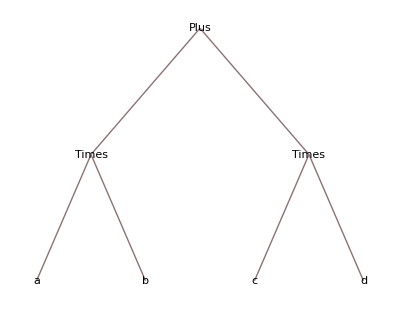

```mathematica
TreeForm[a b+c d]
```

```mathematica
TraditionalForm[a b+c d]
```

a b+c d

```mathematica
a=10+20-15;
2^a+3^a+4^a
```

1088123499

```mathematica
Clear[a]
```

```mathematica
Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[i^2,{i,1,10,1}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[π,10]
```

{π,π,π,π,π,π,π,π,π,π}

```mathematica
Table[{i^2,i^2},{i,1,10,1}]
```

{{1,1},{4,4},{9,9},{16,16},{25,25},{36,36},{49,49},{64,64},{81,81},{100,100}}

```mathematica
StringJoin["The first part","and the second part"]
```

The first partand the second part

```mathematica
ToString[N[π^2]]
```

9.8696

```mathematica
FullForm[%]
```

"9.8696"

```mathematica
StringJoin["π squared is:",ToString[N[π^2]]]
```

π squared is:9.8696

```mathematica
"π squared is:"<>ToString[N[π^2]]
```

π squared is:9.8696

```mathematica
(10m)/s 5s
```

50 m

单位设置：

```mathematica
Quantity[2,"Feet"]
```

QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[2,Feet]]

```mathematica
Quantity[2,"Feet"]+Quantity[3,"Meters"]
```

QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[2,Feet]]+QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[3,Meters]]

```mathematica
UnitConvert[%,"Meters"]
```

UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[2,Feet]]+QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[3,Meters]],Meters]

```mathematica
Quantity[7,"days"]+Quantity[2,"Weeks"]
```

QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[2,Weeks]]+QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[7,days]]

```mathematica
Today
```

Day: Fri 25 Jan 2019

```mathematica
DateList[DateObject[{2016,7,15}]]
```

{2016,7,15,0,0,0.}

```mathematica
DatePlus[Today,7]
```

Day: Fri 1 Feb 2019

```mathematica
DatePlus[Today,Quantity[7,"days"]]
```

DatePlus::inc: QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[7,days]] 不是 DatePlus 的识别出的日历增量指定.

DatePlus[Day: Fri 25 Jan 2019,QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[7,days]]]

```mathematica
DayName[DatePlus[Today,Quantity[4,"Weeks"]]]
```

DatePlus::inc: QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[4,Weeks]] 不是 DatePlus 的识别出的日历增量指定.

DayName::date: 表达式 DatePlus[Day: ,QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[4,Weeks]]] 无法解释为日期指定.

DayName[DatePlus[Day: Fri 25 Jan 2019,QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[4,Weeks]]]]

```mathematica
f[x_]:=x^2
```

```mathematica
f[2]
```

4

```mathematica
f[π]
```

π^2

```mathematica
f[{1,2,3}]
```

{1,4,9}

```mathematica
h[a_,b_]:=a^b
```

```mathematica
h[10,10]
```

10000000000